```mathematica
(*delta term 是没有乘上图的振幅所带的正负I的系数的*)
```

```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-b-dleta-up-xi1.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];

Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
```

```mathematica
Plot3D[I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.037}]
```

-Graphics3D-

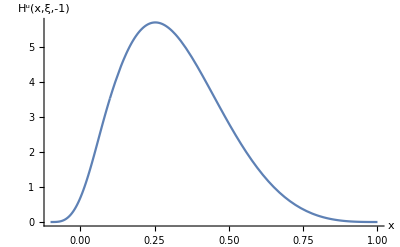

```mathematica
H2d=Show [Plot [-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herf[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H^u(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

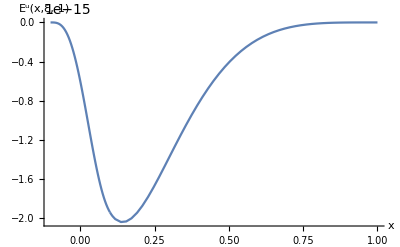

```mathematica
E2d=Show [Plot [-I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerf[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E^u(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

```mathematica
pathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test\\delta",
"b-Hu-2d-0.1.pdf"}];
pathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test\\delta",
"b-Eu-2d-0.1.pdf"}];
```

```mathematica
Export[pathH,H2d]
Export[pathE,E2d]
```

G:\calc-online\gpd\3dre\228test\delta\b-Hu-2d-0.1.pdf

G:\calc-online\gpd\3dre\228test\delta\b-Eu-2d-0.1.pdf